# Constructing the Sets

## How we made the sets G_k

Given a graph G (here we label it the variable d) one can parse it through the following code which will automatically produce the set G_k which is labelled under graphpolyd. Then the last line of code computes the reduced Groebner basis while also timing how long it takes.

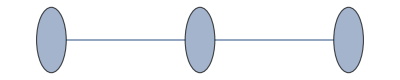

{0.000651,{x2^3+x2^2 x3+x2 x3^2+x3^3,x1^3+x1^2 x2+x1 x2^2-x2^2 x3-x2 x3^2-x3^3,-1+x3^4}}

```mathematica
d=Graph[{{1,2},{2,3}},VertexLabels-> Placed[Automatic,Center],VertexSize-> 0.2]

k=4; 

vert=VertexList[d];
absvert=Length[vert];

edge=EdgeList[d];
edge=List @@@%;
absedge=Length[edge];

vertpoly={};
For[i=1,i≤absvert,i++,AppendTo[vertpoly,Indexed[x,i]^k-1]]

vars=Variables[vertpoly];

edgepoly={};
For[i=1,i≤absedge,i++,AppendTo[edgepoly,Part[PolynomialReduce[Indexed[x,Part[Part[edge,i],1]]^k-Indexed[x,Part[Part[edge,i],2]]^k,Indexed[x,Part[Part[edge,i],1]]-Indexed[x,Part[Part[edge,i],2]],{Indexed[x,Part[Part[edge,i],1]],Indexed[x,Part[Part[edge,i],2]]}],1]]];
edgepoly=Flatten[edgepoly];

graphpolyd=Join[vertpoly,edgepoly];

{test,testgrob}=AbsoluteTiming[GroebnerBasis[graphpolyd,vars,MonomialOrder->DegreeReverseLexicographic]]
```

## How we made the polynomial P_G

After constructing the edge set from the graph, this step is fairly simple as one can take each edge and make it an index using the following code.

```mathematica
Pg=Expand[Product[Indexed[v,Part[Part[edge,i],1]]-Indexed[v,Part[Part[edge,i],2]],{i,1,Length[edgepoly]}]]
```

v1 v2-v2^2-v1 v3+v2 v3

Then from here the ideal we consider in the context of this polynomial P_G is simply generated by the set labelled vertpoly.

```mathematica
vertpoly
```

{-1+x1^4,-1+x2^4,-1+x3^4}